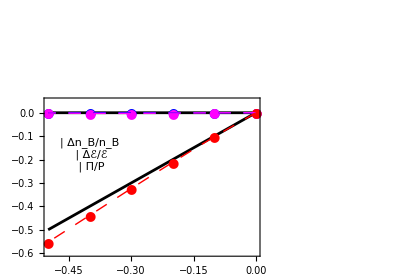

```mathematica
(* Π *)

(*LHC Pb+Pb 5.02 TeV*)

T = 158.4;
μB =0.90; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.00049974,-0.0015779,-0.0025307,-0.0025544,-0.00072888};

PioverPdata = {0.0,-0.10308,-0.21152,-0.32391,-0.43843,-0.55278};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};



legend1=Panel[Grid[{{Graphics[{Blue,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},

{Graphics[{RGBColor[1,0,0],Disk[]},ImageSize->10],Style["Π/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["LHC Pb+Pb   √s = 5.02 TeV",FontSize->16,FontFamily->"Times"]}}],Background->White];


legend2=Panel[Grid[{{Style["T_CF = 158.4 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 0.9 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot  = Table[{frac[[i]],PioverPdata [[i]]},{i,1,Length[frac]}];


pi1=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{-0.4,-0.18}],Inset[legend3,{0.2,0.43}]},ImageSize->{400,300}]
```

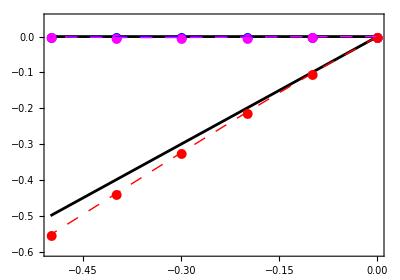

```mathematica
T = 158.384;
μB =22.3; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.00050438,-0.0015958,-0.0025693,-0.0026194,-0.00082375};

PioverPdata = {0.0,-0.10309,-0.21157,-0.32403,-0.43863,-0.55307};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot  = Table[{frac[[i]],PioverPdata [[i]]},{i,1,Length[frac]}];

pi2=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,300}]
```

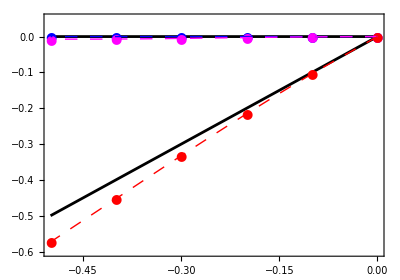

```mathematica
T = 154.7;
μB =218.6; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.00080299,-0.0027575,-0.0050912,-0.0069033,-0.007187};

PioverPdata = {0.0,-0.10409,-0.21544,-0.33235,-0.4526,-0.57325};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot  = Table[{frac[[i]],PioverPdata [[i]]},{i,1,Length[frac]}];

pi3=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,300}]
```

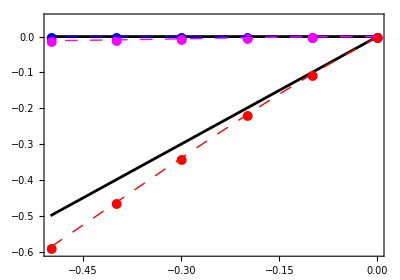

```mathematica
T = 115.1;
μB =535.9; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.00088149,-0.0031544,-0.0061877,-0.0092508,-0.011494};

PioverPdata = {0.0,-0.10501,-0.21882,-0.33921,-0.46338,-0.58775};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot  = Table[{frac[[i]],PioverPdata [[i]]},{i,1,Length[frac]}];

pi4=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"Π/P"}],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"Π/P"}],ListLinePlot[{ΔnBovernBplot,Δϵoverϵplot,PioverPplot},PlotRange->{-0.6,0.05},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"Π/P"}]}
},ImageSize->{400,300}]
```

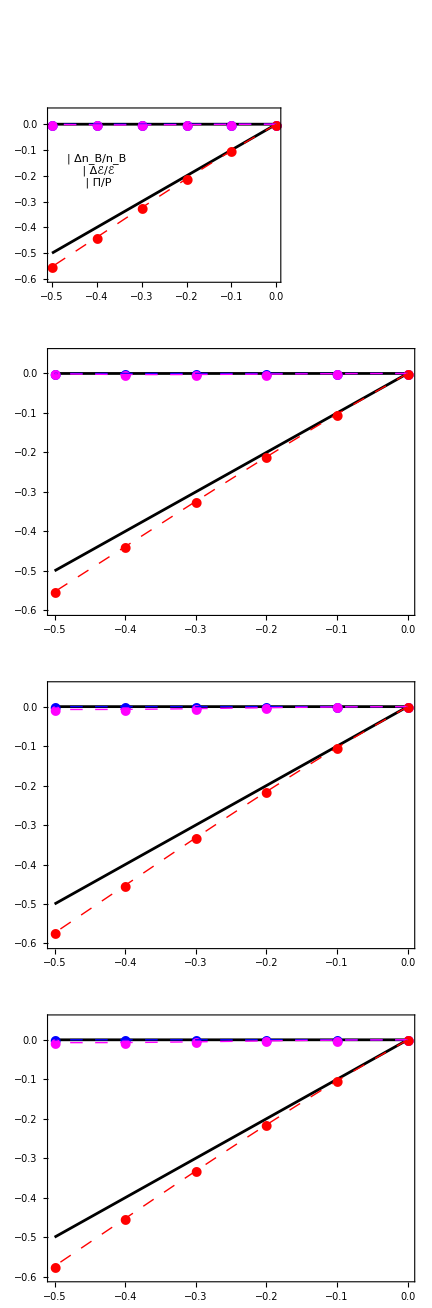

Pitotal.pdf

```mathematica
Pitotal=GraphicsGrid[{{pi1},{pi2},{pi3},{pi4}}]

Export["Pitotal.pdf",pitotal]
```